```mathematica
theKey=epsilon1Key
```

31714

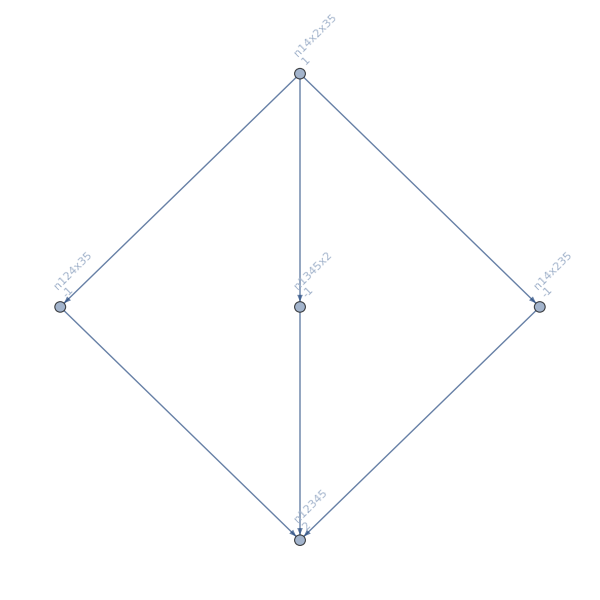

```mathematica
MobiusGraph[theKey]
```

```mathematica
edges=Rest[Map[If[ ToString[#[[0]]]=="GreaterEqual",DirectedEdge[#[[1]], #[[2]]]->Red,DirectedEdge[#[[1]], #[[2]]]->Darker[Green]]&, Map[Simplify[#]&,Select[ineqs2,Length[ListofVars[#]]==2&]]]]
```

{n1x2345->n12345→RGBColor[0, Rational[2, 3], 0],n15x234->n12345→RGBColor[0, Rational[2, 3], 0],n1x234x5->n1234x5→RGBColor[0, Rational[2, 3], 0],n14x235->n12345→RGBColor[1, 0, 0],n145x23->n12345→RGBColor[0, Rational[2, 3], 0],n14x23x5->n1234x5→RGBColor[0, Rational[2, 3], 0],n1x235x4->n1235x4→RGBColor[0, Rational[2, 3], 0],n15x23x4->n1235x4→RGBColor[0, Rational[2, 3], 0],n1x23x4x5->n123x4x5→RGBColor[0, Rational[2, 3], 0],n1x23x45->n123x45→RGBColor[0, Rational[2, 3], 0],n13x2x4x5->n123x4x5→RGBColor[0, Rational[2, 3], 0],n13x245->n12345→RGBColor[1, 0, 0],n135x24->n12345→RGBColor[1, 0, 0],n13x24x5->n1234x5→RGBColor[1, 0, 0],n134x2x5->n1234x5→RGBColor[0, Rational[2, 3], 0],n134x25->n12345→RGBColor[1, 0, 0],n1345x2->n12345→RGBColor[0, Rational[2, 3], 0],n13x25x4->n1235x4→RGBColor[1, 0, 0],n135x2x4->n1235x4→RGBColor[0, Rational[2, 3], 0],n13x2x45->n123x45→RGBColor[0, Rational[2, 3], 0],n1x245x3->n1245x3→RGBColor[0, Rational[2, 3], 0],n15x24x3->n1245x3→RGBColor[0, Rational[2, 3], 0],n1x24x3x5->n124x3x5→RGBColor[0, Rational[2, 3], 0],n1x24x35->n124x35→RGBColor[0, Rational[2, 3], 0],n14x2x3x5->n124x3x5→RGBColor[0, Rational[2, 3], 0],n14x25x3->n1245x3→RGBColor[1, 0, 0],n145x2x3->n1245x3→RGBColor[0, Rational[2, 3], 0],n14x2x35->n124x35→RGBColor[0, Rational[2, 3], 0],n1x25x3x4->n125x3x4→RGBColor[0, Rational[2, 3], 0],n1x25x34->n125x34→RGBColor[0, Rational[2, 3], 0],n15x2x3x4->n125x3x4→RGBColor[0, Rational[2, 3], 0],n15x2x34->n125x34→RGBColor[0, Rational[2, 3], 0],n1x2x34x5->n12x34x5→RGBColor[0, Rational[2, 3], 0],n1x2x345->n12x345→RGBColor[0, Rational[2, 3], 0],n1x2x35x4->n12x35x4→RGBColor[0, Rational[2, 3], 0],n1x2x3x45->n12x3x45→RGBColor[0, Rational[2, 3], 0],n12x3x4x5->n123x4x5→RGBColor[0, Rational[2, 3], 0],n12x345->n12345→RGBColor[0, Rational[2, 3], 0],n125x34->n12345→RGBColor[0, Rational[2, 3], 0],n12x34x5->n1234x5→RGBColor[0, Rational[2, 3], 0],n124x3x5->n1234x5→RGBColor[0, Rational[2, 3], 0],n124x35->n12345→RGBColor[1, 0, 0],n1245x3->n12345→RGBColor[0, Rational[2, 3], 0],n12x35x4->n1235x4→RGBColor[0, Rational[2, 3], 0],n125x3x4->n1235x4→RGBColor[0, Rational[2, 3], 0],n12x3x45->n123x45→RGBColor[0, Rational[2, 3], 0],n123x4x5->n1234x5→RGBColor[0, Rational[2, 3], 0],n123x45->n12345→RGBColor[0, Rational[2, 3], 0],n1235x4->n12345→RGBColor[0, Rational[2, 3], 0],n1234x5->n12345→RGBColor[0, Rational[2, 3], 0],n123x4x5->n1235x4→RGBColor[0, Rational[2, 3], 0],n123x4x5->n123x45→RGBColor[0, Rational[2, 3], 0],n12x3x4x5->n124x3x5→RGBColor[0, Rational[2, 3], 0],n12x3x45->n1245x3→RGBColor[0, Rational[2, 3], 0],n125x3x4->n1245x3→RGBColor[0, Rational[2, 3], 0],n12x35x4->n124x35→RGBColor[0, Rational[2, 3], 0],n124x3x5->n1245x3→RGBColor[0, Rational[2, 3], 0],n124x3x5->n124x35→RGBColor[0, Rational[2, 3], 0],n12x3x4x5->n125x3x4→RGBColor[0, Rational[2, 3], 0],n12x34x5->n125x34→RGBColor[0, Rational[2, 3], 0],n125x3x4->n125x34→RGBColor[0, Rational[2, 3], 0],n12x3x4x5->n12x34x5→RGBColor[0, Rational[2, 3], 0],n12x3x45->n12x345→RGBColor[0, Rational[2, 3], 0],n12x35x4->n12x345→RGBColor[0, Rational[2, 3], 0],n12x34x5->n12x345→RGBColor[0, Rational[2, 3], 0],n12x3x4x5->n12x35x4→RGBColor[0, Rational[2, 3], 0],n12x3x4x5->n12x3x45→RGBColor[0, Rational[2, 3], 0],n1x2x3x4x5->n13x2x4x5→RGBColor[0, Rational[2, 3], 0],n1x2x345->n1345x2→RGBColor[0, Rational[2, 3], 0],n15x2x34->n1345x2→RGBColor[0, Rational[2, 3], 0],n1x25x34->n134x25→RGBColor[0, Rational[2, 3], 0],n1x2x34x5->n134x2x5→RGBColor[0, Rational[2, 3], 0],n14x2x3x5->n134x2x5→RGBColor[0, Rational[2, 3], 0],n14x2x35->n1345x2→RGBColor[1, 0, 0],n145x2x3->n1345x2→RGBColor[0, Rational[2, 3], 0],n14x25x3->n134x25→RGBColor[0, Rational[2, 3], 0],n1x24x35->n135x24→RGBColor[0, Rational[2, 3], 0],n1x2x35x4->n135x2x4→RGBColor[0, Rational[2, 3], 0],n15x2x3x4->n135x2x4→RGBColor[0, Rational[2, 3], 0],n15x24x3->n135x24→RGBColor[0, Rational[2, 3], 0],n1x24x3x5->n13x24x5→RGBColor[0, Rational[2, 3], 0],n1x245x3->n13x245→RGBColor[0, Rational[2, 3], 0],n1x25x3x4->n13x25x4→RGBColor[0, Rational[2, 3], 0],n1x2x3x45->n13x2x45→RGBColor[0, Rational[2, 3], 0],n13x2x4x5->n134x2x5→RGBColor[0, Rational[2, 3], 0],n13x2x45->n1345x2→RGBColor[0, Rational[2, 3], 0],n135x2x4->n1345x2→RGBColor[0, Rational[2, 3], 0],n13x25x4->n134x25→RGBColor[0, Rational[2, 3], 0],n134x2x5->n1345x2→RGBColor[0, Rational[2, 3], 0],n134x2x5->n134x25→RGBColor[0, Rational[2, 3], 0],n13x2x4x5->n135x2x4→RGBColor[0, Rational[2, 3], 0],n13x24x5->n135x24→RGBColor[0, Rational[2, 3], 0],n135x2x4->n135x24→RGBColor[0, Rational[2, 3], 0],n13x2x4x5->n13x24x5→RGBColor[0, Rational[2, 3], 0],n13x2x45->n13x245→RGBColor[0, Rational[2, 3], 0],n13x25x4->n13x245→RGBColor[0, Rational[2, 3], 0],n13x24x5->n13x245→RGBColor[0, Rational[2, 3], 0],n13x2x4x5->n13x25x4→RGBColor[0, Rational[2, 3], 0],n13x2x4x5->n13x2x45→RGBColor[0, Rational[2, 3], 0],n1x2x3x4x5->n14x2x3x5→RGBColor[0, Rational[2, 3], 0],n1x23x45->n145x23→RGBColor[0, Rational[2, 3], 0],n1x2x3x45->n145x2x3→RGBColor[0, Rational[2, 3], 0],n15x2x3x4->n145x2x3→RGBColor[0, Rational[2, 3], 0],n15x23x4->n145x23→RGBColor[0, Rational[2, 3], 0],n1x23x4x5->n14x23x5→RGBColor[0, Rational[2, 3], 0],n1x235x4->n14x235→RGBColor[0, Rational[2, 3], 0],n1x25x3x4->n14x25x3→RGBColor[0, Rational[2, 3], 0],n1x2x35x4->n14x2x35→RGBColor[0, Rational[2, 3], 0],n14x2x3x5->n145x2x3→RGBColor[0, Rational[2, 3], 0],n14x23x5->n145x23→RGBColor[0, Rational[2, 3], 0],n145x2x3->n145x23→RGBColor[0, Rational[2, 3], 0],n14x2x3x5->n14x23x5→RGBColor[0, Rational[2, 3], 0],n14x2x35->n14x235→RGBColor[0, Rational[2, 3], 0],n14x25x3->n14x235→RGBColor[0, Rational[2, 3], 0],n14x23x5->n14x235→RGBColor[0, Rational[2, 3], 0],n14x2x3x5->n14x25x3→RGBColor[0, Rational[2, 3], 0],n14x2x3x5->n14x2x35→RGBColor[0, Rational[2, 3], 0],n1x2x3x4x5->n15x2x3x4→RGBColor[0, Rational[2, 3], 0],n1x23x4x5->n15x23x4→RGBColor[0, Rational[2, 3], 0],n1x234x5->n15x234→RGBColor[0, Rational[2, 3], 0],n1x24x3x5->n15x24x3→RGBColor[0, Rational[2, 3], 0],n1x2x34x5->n15x2x34→RGBColor[0, Rational[2, 3], 0],n15x2x3x4->n15x23x4→RGBColor[0, Rational[2, 3], 0],n15x2x34->n15x234→RGBColor[0, Rational[2, 3], 0],n15x24x3->n15x234→RGBColor[0, Rational[2, 3], 0],n15x23x4->n15x234→RGBColor[0, Rational[2, 3], 0],n15x2x3x4->n15x24x3→RGBColor[0, Rational[2, 3], 0],n15x2x3x4->n15x2x34→RGBColor[0, Rational[2, 3], 0],n1x2x3x4x5->n1x23x4x5→RGBColor[0, Rational[2, 3], 0],n1x2x345->n1x2345→RGBColor[0, Rational[2, 3], 0],n1x25x34->n1x2345→RGBColor[0, Rational[2, 3], 0],n1x2x34x5->n1x234x5→RGBColor[0, Rational[2, 3], 0],n1x24x3x5->n1x234x5→RGBColor[0, Rational[2, 3], 0],n1x24x35->n1x2345→RGBColor[1, 0, 0],n1x245x3->n1x2345→RGBColor[0, Rational[2, 3], 0],n1x2x35x4->n1x235x4→RGBColor[0, Rational[2, 3], 0],n1x25x3x4->n1x235x4→RGBColor[0, Rational[2, 3], 0],n1x2x3x45->n1x23x45→RGBColor[0, Rational[2, 3], 0],n1x23x4x5->n1x234x5→RGBColor[0, Rational[2, 3], 0],n1x23x45->n1x2345→RGBColor[0, Rational[2, 3], 0],n1x235x4->n1x2345→RGBColor[0, Rational[2, 3], 0],n1x234x5->n1x2345→RGBColor[0, Rational[2, 3], 0],n1x23x4x5->n1x235x4→RGBColor[0, Rational[2, 3], 0],n1x23x4x5->n1x23x45→RGBColor[0, Rational[2, 3], 0],n1x2x3x4x5->n1x24x3x5→RGBColor[0, Rational[2, 3], 0],n1x2x3x45->n1x245x3→RGBColor[0, Rational[2, 3], 0],n1x25x3x4->n1x245x3→RGBColor[0, Rational[2, 3], 0],n1x2x35x4->n1x24x35→RGBColor[0, Rational[2, 3], 0],n1x24x3x5->n1x245x3→RGBColor[0, Rational[2, 3], 0],n1x24x3x5->n1x24x35→RGBColor[0, Rational[2, 3], 0],n1x2x3x4x5->n1x25x3x4→RGBColor[0, Rational[2, 3], 0],n1x2x34x5->n1x25x34→RGBColor[0, Rational[2, 3], 0],n1x25x3x4->n1x25x34→RGBColor[0, Rational[2, 3], 0],n1x2x3x4x5->n1x2x34x5→RGBColor[0, Rational[2, 3], 0],n1x2x3x45->n1x2x345→RGBColor[0, Rational[2, 3], 0],n1x2x35x4->n1x2x345→RGBColor[0, Rational[2, 3], 0],n1x2x34x5->n1x2x345→RGBColor[0, Rational[2, 3], 0],n1x2x3x4x5->n1x2x35x4→RGBColor[0, Rational[2, 3], 0],n1x2x3x4x5->n1x2x3x45→RGBColor[0, Rational[2, 3], 0]}

```mathematica
g=MobiusGraph[theKey];
```

```mathematica
base=Map[If[ ToString[#[[0]]]=="GreaterEqual",DirectedEdge[#[[1]], #[[2]]]->{Thick,Red}, DirectedEdge[#[[1]], #[[2]]]->{Darker[Green]}]&, Map[Simplify[#]&,Select[ineqs2,Length[ListofVars[#]]==2&]]];
```

```mathematica
edges=Select[base,MemberQ[EdgeList[g],#[[1]]]&];
```

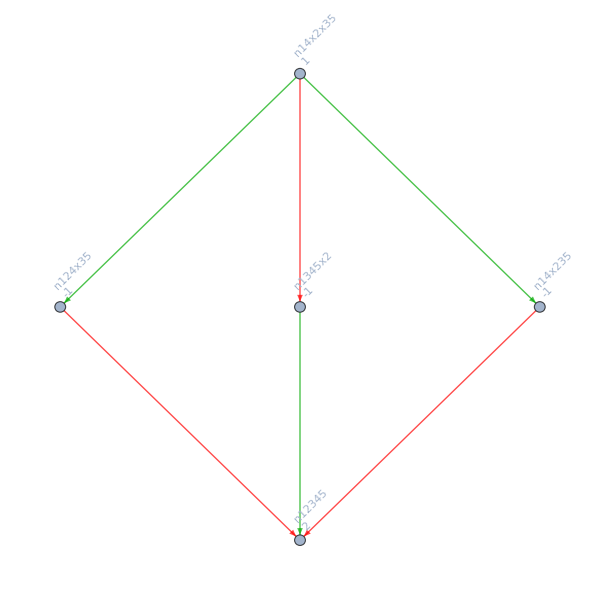

```mathematica
Graph[g,EdgeStyle->edges]
```

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Select[Keys[allGraphs],MemberQ[{n14x2x35,n1345x2},allGraphs[#,"colofourrealnull"]]&]}]
```

{-Graphics-18980,-Graphics-4380}

```mathematica
Table[Labeled[allGraphs[k,"graph"],allGraphs[k,"compwhy"]],{k,{24144,43908}}]
```

{-Graphics-The relation holds x24144== x31444(GreaterEqual) + 39014 (Greater),-Graphics-The relation holds x43908== x51478(GreaterEqual) + 59048 (Greater)}

```mathematica
allGraphs[24144,"vertexsets"]
```

{{1,4},{2},{3,5}}

```mathematica
Table[Labeled[allGraphs[k,"graph"],Style[k,ColourForKey[allGraphs,k]]],{k,Select[Keys[allGraphs],allGraphs[#,"vertexsets"]=={{1,4},{2},{3,5}}&]}]
```

{-Graphics-31714,-Graphics-31444,-Graphics-24414,-Graphics-24144,-Graphics-11950,-Graphics-11680,-Graphics-4650,-Graphics-4380}